```mathematica
(*check if torus cycle with the plaquettes is the fundamendal cycle basis and 
if so if every ground state is correct for a corresponding realization in which
the torus has different parity edges by flipping the edges cutting the torus band. *)
```

```mathematica
ClearAll["Global`*"];Clear[Derivative];
SetDirectory["/Users/tosku/Documents/sggs/"];
Import[NotebookDirectory[]<>"lattice.wl"];
L=6;
d=2;

latticeFile="cologne/L6real3.lattice";
OpenRead[latticeFile];
ledgelist=ReadList[latticeFile, {Number,Number,Number}];
Close[latticeFile];
lattice=Graph[listToEdges[{#[[1]],#[[2]]}&/@ledgelist],EdgeWeight->First[{Last[#]&/@ledgelist}]];
Jij[lattice,#]&/@EdgeList[lattice]
```

{1,-1,1,-1,-1,1,-1,1,-1,-1,1,1,-1,-1,-1,-1,1,-1,1,-1,1,-1,1,1,1,1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,1,1,-1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,1,1,1,1,-1,1,-1,1,-1}

```mathematica
(*lattice=getPCBLattice[L,d];*)

nV[i_,j_,L_]:=nextVertex[i,j,L]
pV[i_,j_,L_]:=previousVertex[i,j,L]
```

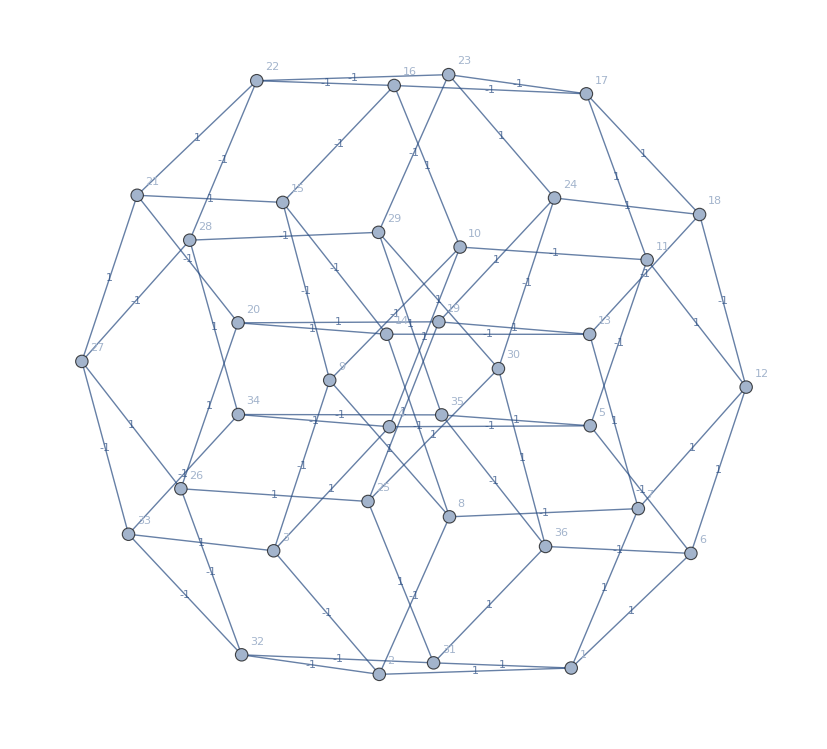

```mathematica
lattice//labelVertices//labelEdges
```

```mathematica
(*Function to map Plaquettes as lists of edges *)
plaquetteOfVertexInPlane[i_,plane_,L_]:=
Fold[If[#1=={},
Append[#1,{i,nV[i,#2,L]}],
If[NumericQ[Last[Last[#1]]],
Append[#1,{Last[Last[#1]],
If[Length[#1]<2,
nV[Last[Last[#1]],#2,L],
pV[Last[Last[#1]],#2,L]
]}
],Append[#1,{Last[Last[#1]],False}]]
]&,{},Join[plane,plane]]
```

```mathematica
isPlaquette[plaquette_]:=Fold[If[#1==True&&NumericQ[First[#2]]&&NumericQ[Last[#2]],True,False]&,True,plaquette]
```

```mathematica
getInternalPlaquettes[L_,d_]:=Select[Sort[Flatten[Map[Function[vl,plaquetteOfVertexInPlane[vl,#,L]&/@Subsets[Range[1,d],{2}]][#]&,Range[1,L^d]],1]],isPlaquette];
```

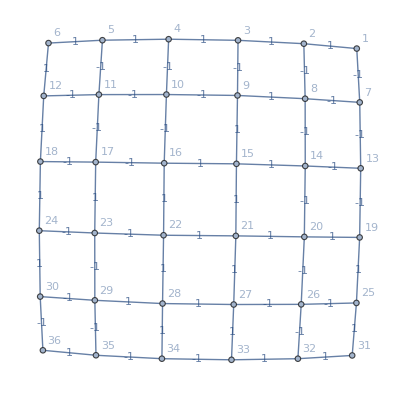

```mathematica
getFreeBoundaryLattice[L,d]//labelVertices//labelEdges
```

```mathematica
EdgeCount[lattice]
```

72

```mathematica
(* todo test for all d 
countTest[plaqs_,d_]:=
If[d==2,Length[plaqs]==(L-1)^d,If[d==3,2d(L-1)^d/2+2d*(L-1)^2/2,"no test yet"]]
*)
```

```mathematica
isFrustrated[graph_,cycle_]:= Fold[#1*Jij[graph, Apply[UndirectedEdge,#2]]&,1,cycle]<0;
```

```mathematica
totalFrustration[graph_,cycles_]:=Length[Select[cycles,isFrustrated[graph,#]&]];
totalFrustration[lattice,getInternalPlaquettes[L,d]]
```

18

```mathematica
N[totalFrustration[lattice,getInternalPlaquettes[L,d]]/Length[getInternalPlaquettes[L,d]]]
```

0.5

```mathematica
labelCycles[cycles_]:=MapThread[List,{Range[1,Length[cycles]],cycles}]
```

```mathematica
(* basic subgraphs of a barahona city as edge lists *)
getXNOR[label_]:={{Append[label,1],Append[label,2]},{Append[label,2],Append[label,3]},{Append[label,3],Append[label,1]}};
```

```mathematica
getXOR[label_]:={{Append[label,1],Append[label,4]},{Append[label,4],Append[label,6]},{Append[label,4],Append[label,5]},{Append[label,5],Append[label,6]},{Append[label,5],Append[label,2]},{Append[label,6],Append[label,3]}};
```

```mathematica
addNeighborhoods[na_, nb_]:=Apply[UndirectedEdge,#]&/@Append[Join[na,nb],{Flatten[{Take[First[First[na]],Length[First[First[na]]]-1],3}],Flatten[{Take[First[First[nb]],Length[First[First[nb]]]-1],3}]}];
```

```mathematica
getCompName[component_]:=If[Length[component]>6,
First[First[First[component]]],
Take[First[First[component]],Length[First[First[component]]]-1]
];
```

```mathematica
getFreeVertices[component_]:=
Sort[Complement[Complement[DeleteDuplicates[Flatten[component,1]],
DeleteDuplicates[Select[Flatten[component,1],Count[Flatten[component,1],#]==3&]],DeleteDuplicates[Flatten[Select[component,(Last[First[#]]==3||Last[Last[#]]==3)&&First[#][[2]]≠Last[#][[2]]&],1]]]]]
```

```mathematica
getBiggerFreeVertex[component_]:=Last[getFreeVertices[component]]
```

```mathematica
addComponents[componentList_]:=Fold[If[Length[#1]==0,#2,Join[#1,Append[#2,{getBiggerFreeVertex[#1],getBiggerFreeVertex[#2]}]]]&,{},componentList]
```

```mathematica
(*plaquetteToBarahonaCity*)
```

```mathematica
edgeListOfBarahonaCity[Lattice_,plaquetteName_,plaquetteEdges_]:=If[isFrustrated[Lattice,plaquetteEdges],
addComponents[Fold[Append[#1,getXOR[{plaquetteName,#2}]]&,{getXNOR[{plaquetteName,1}]},Range[2,Length[plaquetteEdges]-2]]],
addComponents[Fold[Append[#1,getXOR[{plaquetteName,#2}]]&,{},Range[1,Length[plaquetteEdges]-2]]]
]
```

```mathematica
plaquettesToBarahonaCities[lattice_,L_,d_]:=edgeListOfBarahonaCity[lattice,First[#],Last[#]]&/@labelCycles[getInternalPlaquettes[L,d]]
```

```mathematica
cityList=plaquettesToBarahonaCities[lattice,L,d];
```

```mathematica
findAdjacentPlaquette[edge_,plaquettes_]:=Select[labelCycles[plaquettes],Length[Position[#,Reverse[edge]]]≠0||Length[Position[#,edge]]≠0&]
```

```mathematica
intraPlaquetteEdges[plaquettes_,edges_]:=Select[Fold[Append[#1,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]]&,{},edges],Length[#]>1&]
```

```mathematica
plaquetteToLEdges[plaquetteName_,L_,d_]:=Last[Last[Select[labelCycles[getInternalPlaquettes[L,d]],First[#]==plaquetteName&]]];
```

```mathematica
getCityOfPlaquette[cityList_,plaquetteName_]:=Select[cityList,getCompName[#]==plaquetteName&];
```

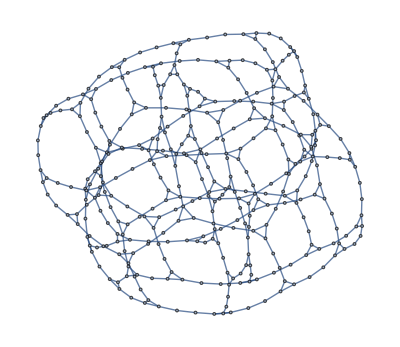

```mathematica
getVertexFromList[cityList_,name_]:=SelectFirst[cityList,First[#]==name&];
getEdgeFromFreeList[freeList_,edge_]:=Fold[Append[#1, getVertexFromList[Complement[freeList,#1],#2]]&,{}, edge]

intraCityEdges[cityList_,cityEdges_]:=Fold[
Append[#1,getEdgeFromFreeList[Complement[Flatten[getFreeVertices[#]&/@cityList,1],Flatten[#1,1]],#2]]
&,{},cityEdges];

boundaryCityEdges[plaquettes_,edges_]:=Append[Last[#],0]&/@Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]}]&,{},edges],Length[Last[#]]<2&]

boundaryEdges[plaquettes_,edges_]:=First[#]&/@Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]}]&,{},edges],Length[Last[#]]<2&]

boundaryLEdgePlaquetteList[L_,d_,lattice_]:=Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],getInternalPlaquettes[L,d]]]}]&,{},EdgeList[lattice]],Length[Last[#]]<2&]

makeBoundaryCycle[plaquettes_,lattice_]:=edgeListOfBarahonaCity[lattice,0,boundaryEdges[plaquettes,Apply[List,#]&/@EdgeList[lattice]]]

(* Matching graph for pbc lattices
matchingGraphEdgeList[lattice_,L_,d_]:=Join[intraCityEdges[plaquettesToBarahonaCities[lattice,L,d],intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]
,Flatten[plaquettesToBarahonaCities[lattice,L,d],1]] *)

JEdges[lattice_,L_,d_]:=intraCityEdges[
plaquettesToBarahonaCities[lattice,L,d],Join[intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]]

(* Matching dual graph for 2d free boundary lattice ]*)
matchingGraphEdgeList[lattice_,L_,d_]:=
Join[intraCityEdges[plaquettesToBarahonaCities[lattice,L,d],intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]
,Flatten[plaquettesToBarahonaCities[lattice,L,d],1]]

zeroWeights[mgraph_]:=Fold[SetProperty[{#1,#2},EdgeWeight->0]&,mgraph,EdgeList[mgraph]]
addWeights[mgraph_,lattice_,L_,d_]:=Fold[SetProperty[{#1,#2},EdgeWeight->1]&,mgraph,Apply[UndirectedEdge,#]&/@JEdges[lattice,L,d]]
(*Creates Mapped Graph M from the given Lattice *)
M=addWeights[zeroWeights[Graph[listToEdges[matchingGraphEdgeList[lattice,L,d]]]],lattice,L,d]
```

```mathematica
JEdges[lattice,L,d]
```

{{{1,1,1},{31,1,1}},{{2,1,1},{32,1,1}},{{3,1,1},{33,1,1}},{{4,1,1},{34,1,1}},{{5,1,1},{35,1,1}},{{6,1,1},{36,1,1}},{{1,1,2},{7,1,1}},{{2,1,2},{8,1,1}},{{3,1,2},{9,1,1}},{{4,1,2},{10,1,1}},{{5,1,2},{11,1,1}},{{6,1,2},{12,1,1}},{{7,1,2},{13,1,1}},{{8,1,2},{14,1,1}},{{9,1,2},{15,1,1}},{{10,1,2},{16,1,1}},{{11,1,2},{17,1,1}},{{12,1,2},{18,1,1}},{{13,1,2},{19,1,1}},{{14,1,2},{20,1,1}},{{15,1,2},{21,1,1}},{{16,1,2},{22,1,1}},{{17,1,2},{23,1,1}},{{18,1,2},{24,1,1}},{{19,1,2},{25,1,1}},{{20,1,2},{26,1,1}},{{21,1,2},{27,1,1}},{{22,1,2},{28,1,1}},{{23,1,2},{29,1,1}},{{24,1,2},{30,1,1}},{{25,1,2},{31,1,2}},{{26,1,2},{32,1,2}},{{27,1,2},{33,1,2}},{{28,1,2},{34,1,2}},{{29,1,2},{35,1,2}},{{30,1,2},{36,1,2}},{{1,2,1},{6,2,1}},{{1,2,2},{2,2,1}},{{2,2,2},{3,2,1}},{{3,2,2},{4,2,1}},{{4,2,2},{5,2,1}},{{5,2,2},{6,2,2}},{{7,2,1},{12,2,1}},{{7,2,2},{8,2,1}},{{8,2,2},{9,2,1}},{{9,2,2},{10,2,1}},{{10,2,2},{11,2,1}},{{11,2,2},{12,2,2}},{{13,2,1},{18,2,1}},{{13,2,2},{14,2,1}},{{14,2,2},{15,2,1}},{{15,2,2},{16,2,1}},{{16,2,2},{17,2,1}},{{17,2,2},{18,2,2}},{{19,2,1},{24,2,1}},{{19,2,2},{20,2,1}},{{20,2,2},{21,2,1}},{{21,2,2},{22,2,1}},{{22,2,2},{23,2,1}},{{23,2,2},{24,2,2}},{{25,2,1},{30,2,1}},{{25,2,2},{26,2,1}},{{26,2,2},{27,2,1}},{{27,2,2},{28,2,1}},{{28,2,2},{29,2,1}},{{29,2,2},{30,2,2}},{{31,2,1},{36,2,1}},{{31,2,2},{32,2,1}},{{32,2,2},{33,2,1}},{{33,2,2},{34,2,1}},{{34,2,2},{35,2,1}},{{35,2,2},{36,2,2}}}

```mathematica
findAdjacentPlaquette[#,getInternalPlaquettes[L,d]]&/@EdgeList[lattice]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
(*Test for matching map total weight should equal the number of lattice edges*)Total[PropertyValue[{M,#},EdgeWeight]&/@EdgeList[M]]==EdgeCount[lattice]
```

True

```mathematica
(*create NM Edgelist with normalized edge labels of M *)relabelEdges[graph_]:={First[First[Position[VertexList[graph],First[#]]]]-1,First[First[Position[VertexList[graph],Last[#]]]]-1,PropertyValue[{graph,#},EdgeWeight]}&/@EdgeList[graph];

(*debugrelabelEdges[graph_]:={{First[#],Last[#]},First[First[Position[VertexList[graph],First[#]]]]-1<->First[First[Position[VertexList[graph],Last[#]]]]-1}&/@EdgeList[graph];*)

NMEdgeToMEdge[NMEdge_,MGraph_]:={VertexList[MGraph][[First[NMEdge]+1]],VertexList[MGraph][[Last[NMEdge]+1]]};
```

```mathematica
stringifyGraph[graph_]:=ToString[VertexCount[graph]]<>" "<>ToString[EdgeCount[graph]]<>"\n"<>Fold[If[#1==3,#2<>"\n",#1<>ToString[#2]<>"\n"]&,3,ToString[#[[1]]]<>" "<>ToString[#[[2]]]<>" "<>ToString[#[[3]]]&/@relabelEdges[graph]];
```

```mathematica
stringifyGraphForCologne[graph_]:=Fold[If[#1==3,#2<>"\n",#1<>ToString[#2]<>"\n"]&,3,ToString[#[[1]]]<>" "<>ToString[#[[2]]]<>" "<>ToString[#[[3]]]&/@Sort[{First[#],Last[#],PropertyValue[{graph,#},EdgeWeight]}&/@EdgeList[graph]]];
```

```mathematica
basename="~/Documents/sggs/"<>DateString["ISODateTime"]<>"_L"<>ToString[L]<>"_d"<>ToString[d];
```

```mathematica
NM=Graph[UndirectedEdge[#[[1]],#[[2]]]&/@relabelEdges[M]]
```

-Graphics-

```mathematica
st=OpenWrite[basename<>".matchdual"]
WriteString[st, stringifyGraph[M]]
Close[st]
```

OutputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:04:06_L6_d2.matchdual

```mathematica
lt=OpenWrite[basename<>".lattice"]
WriteString[lt, stringifyGraphForCologne[lattice]]
Close[lt]
```

OutputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:04:06_L6_d2.lattice

```mathematica
Run["blossom5/blossom5 -e "<>basename<>".matchdual -w "<>basename<>".matching"]
```

0

```mathematica
matchfile=OpenRead[basename<>".matching"]
NMatchedEdges=Drop[ReadList[matchfile, {Number,Number}],1];
Close[matchfile]
```

InputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:04:06_L6_d2.matching

```mathematica
NMatched =Graph[listToEdges[NMatchedEdges]];
```

```mathematica
HighlightGraph[NM,NMatched,GraphHighlightStyle->"Thick"];
```

```mathematica
(*Test if matching is perfect*)
Length[VertexList[NMatched]]==Length[VertexList[M]]
```

True

```mathematica
Matched=NMEdgeToMEdge[#,M]&/@NMatchedEdges;
```

```mathematica
HighlightGraph[M,listToEdges[Matched],GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Total[Jij[M,#]&/@listToEdges[Matched]]
```

10

```mathematica
MEdgeToLEdge[MEdge_,MGraph_,lattice_,L_,d_]:=If[First[First[MEdge]]==0||First[Last[MEdge]]==0,
First[edgesToList[First[boundaryLEdgePlaquetteList[L,d,lattice][[First[Position[edgesToList[Select[EdgeList[MGraph],Jij[MGraph,#]≠0&&(First[First[#]]==0||First[Last[#]]==0)&]],MEdge]]]]]]]
,First[Select[plaquetteToLEdges[First[First[MEdge]],L,d],Length[Position[plaquetteToLEdges[First[Last[MEdge]],L,d],#]]≠0||Length[Position[plaquetteToLEdges[First[Last[MEdge]],L,d],Reverse[#]]]≠0&]]]

UnsatisfiedEdges[L_,d_,lattice_,MGraph_,MatchedEdges_]:=MEdgeToLEdge[#,MGraph,lattice,L,d]&/@edgesToList[Select[listToEdges[MatchedEdges],First[First[#]]≠First[Last[#]]&]];
Jij[lattice,Apply[UndirectedEdge,{14,15}]]
```

-1

```mathematica
unsatisfiedEdgesToSpins[unsatisfiedEdges_,lattice_,i_]:=Fold[If[Spin[First[#2],#1]==0,
ReplacePart[#1,First[#2]->Spin[Last[#2],#1]*Sign[Jij[lattice,#2]]],
ReplacePart[#1,Last[#2]->Spin[First[#2],#1]*Sign[Jij[lattice,#2]]]]&,ReplacePart[ConstantArray[0,VertexCount[lattice]],i->1],Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],i,{"FrontierEdge"->Sow}]]⟦2,1⟧];
latticeMinCut=UnsatisfiedEdges[L,d,lattice,M,Matched]
GS=unsatisfiedEdgesToSpins[latticeMinCut,lattice,5];

unsatisfiedEdgesFromSpins[lattice_,configuration_]:=Fold[If[Spin[First[#2],configuration]*Jij[lattice,#2]*Spin[Last[#2],configuration]<0,Append[#1,#2],#1]&,{},EdgeList[lattice]]

unsatisfiedEdgesToSpins[latticeMinCut,lattice,#]&/@VertexList[lattice];
Energy[lattice,unsatisfiedEdgesToSpins[latticeMinCut,lattice,#]]&/@VertexList[lattice]

-EdgeCount[lattice]+2 Length[latticeMinCut]

{Energy[lattice,GS]/VertexCount[lattice],(-EdgeCount[lattice]+2 Length[latticeMinCut])/VertexCount[lattice]}//N
unsatisfiedEdgesFromSpins[lattice,GS]
```

{{2,3},{4,5},{14,13},{18,17},{19,24},{27,26},{9,15},{28,34},{29,35},{36,6}}

{-44,-44,-44,-44,-48,-48,-44,-44,-44,-44,-48,-48,-44,-48,-44,-44,-44,-40,-44,-44,-44,-44,-44,-48,-44,-44,-48,-40,-44,-48,-44,-44,-44,-44,-44,-48}

-52

{-1.33333,-1.44444}

{4<->5,8<->9,13<->14,14<->15,17<->18,20<->21,24<->19,32<->33,9<->15,28<->34,29<->35,36<->6}

```mathematica
edgesToList[Reap[BreadthFirstScan[GraphDifference[lattice,Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧]
```

{{1,2},{1,7},{6,1},{31,1},{2,8},{32,2},{7,13},{12,7},{5,6},{25,31},{36,31},{8,9},{8,14},{26,32},{32,33},{13,19},{18,13},{11,12},{35,5},{30,25},{3,9},{9,10},{14,15},{14,20},{27,33},{33,34},{18,24},{11,17},{29,30},{3,4},{10,16},{15,21},{27,28},{23,24},{16,22}}

```mathematica
labelVertices[lattice]//labelEdges;
```

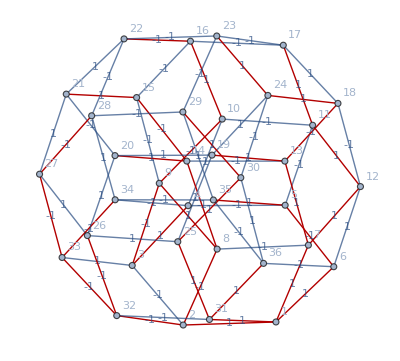

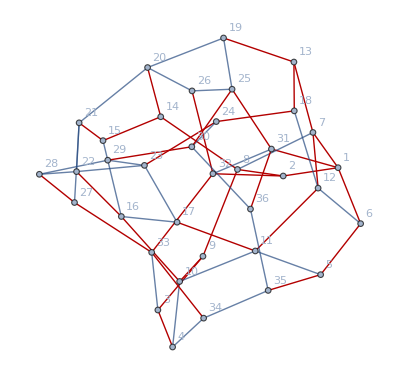

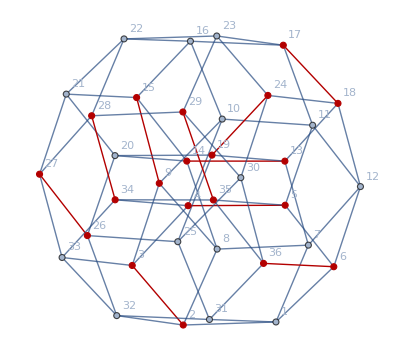

```mathematica
Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧//HighlightGraph[%,#]&

Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧//HighlightGraph[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],#]&//labelVertices

HighlightGraph[lattice,Graph[listToEdges[latticeMinCut]]]//labelVertices
```

```mathematica
(*BFS for spinconf*)
```